## Graph

## Basic Examples

An undirected graph:



```mathematica
Graph[{1<->2,2<->3,3<->1}]
```

A directed graph:

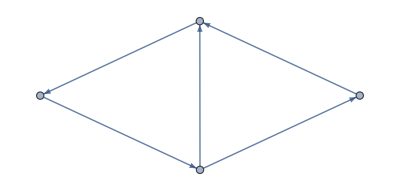

```mathematica
Graph[{1->2,2->3,3->4,4->1,2->4}]
```

Style vertexes and edges:

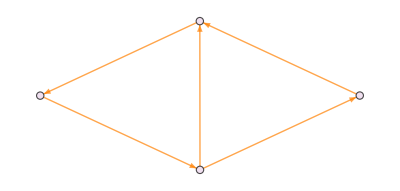

```mathematica
Graph[{1->2,2->3,3->4,4->1,2->4},VertexStyle->LightPurple,EdgeStyle->Orange]
```

Use wrappers to input directly:

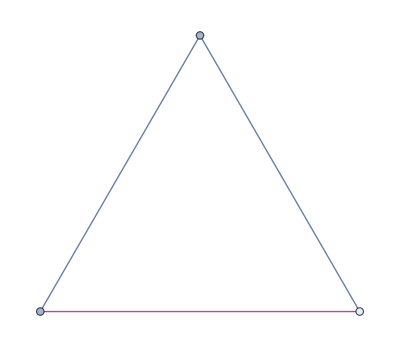

```mathematica
Graph[{1,2,Style[3,LightBlue]},{1<->2,2<->3,Style[3<->1,Purple]}]
```

Label vertices and edges:

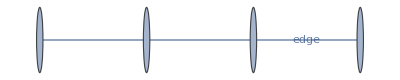

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->4,"edge"]}]
```

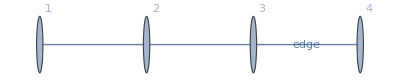

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->4,"edge"]},VertexLabels->"Name"]
```

Use different vertices and edges:

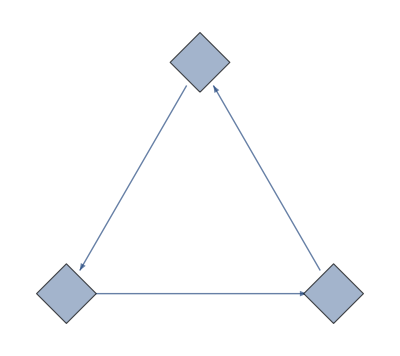

```mathematica
Graph[{1->2,2->3,3->1},VertexShapeFunction->"Diamond",VertexSize->Medium]
```

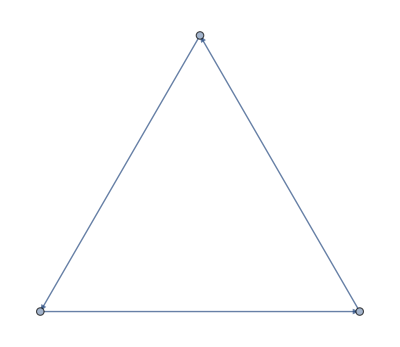

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->"CarvedArcArrow"]
```

## Options

### AnnotationRules

Specify an annotation for vertices:

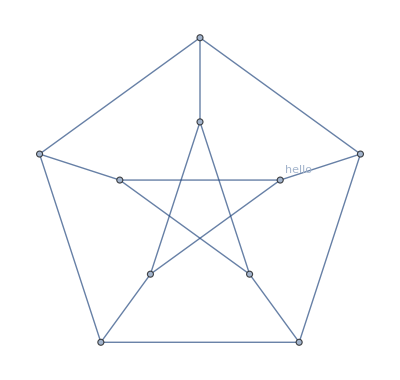

```mathematica
Graph[PetersenGraph[],AnnotationRules->{1->{VertexLabels->"hello"}}]
```

Edges:

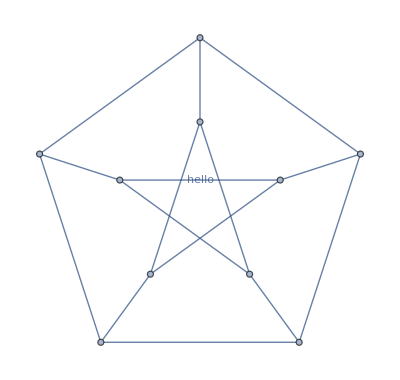

```mathematica
Graph[PetersenGraph[],AnnotationRules->{1<->4->{EdgeLabels->"hello"}}]
```

### DirectedEdges

By default, a directed graph is generated when giving a list of rules:



```mathematica
Graph[{1->2,2->3,3->1}]
```

Use DirectedEdges->False to interpret rules as undirected edges:

```mathematica
Graph[{1->2,2->3,3->1},DirectedEdges->False]
```

-Graphics-

Use DirectedEdge or UndirectedEdge to specify whether a graph is directed or not:

### EdgeLabels

```mathematica
{Graph[{1->2,2->3,3->1}],Graph[{1<->2,2<->3,3<->1}]}
```

{-Graphics-,-Graphics-}

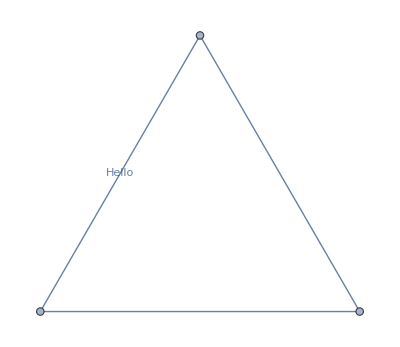

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->"Hello"}]
```

```mathematica
el={1<->2,2<->3,3<->1};
```

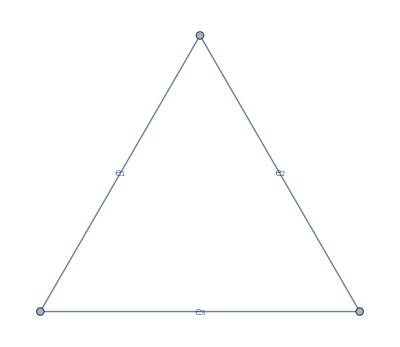

```mathematica
Graph[el,EdgeLabels->Table[el[[i]]->Subscript[e, i],{i,Length[el]}]]
```

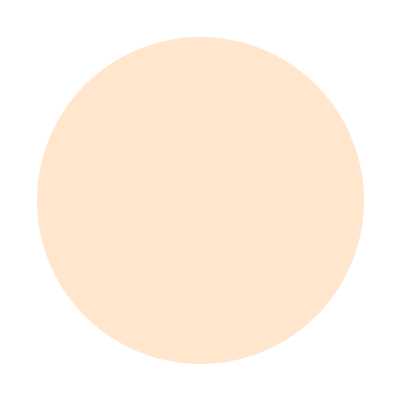
{-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
edgeLabelImages=Graphics[#,ImageSize->Tiny]&/@{Graphics[{LightOrange,Disk[{3,4}]}],Graphics3D[{Torus[RandomReal[2,{3}],{1,2}]}],PolyhedronData["MathematicaPolyhedron","Image"]}
```

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->-Graphics-,2<->3->-Graphics3D-,3<->1->-Graphics-}]
```

-Graphics-

Use Placed with symbolic locations to control label placement along an edge:

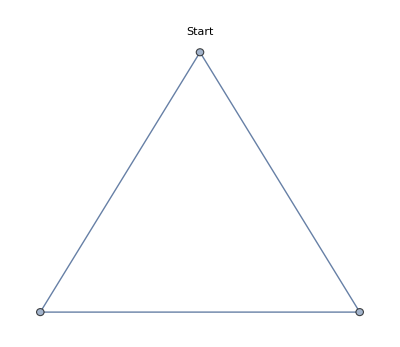
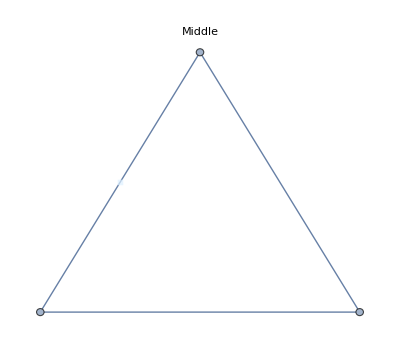
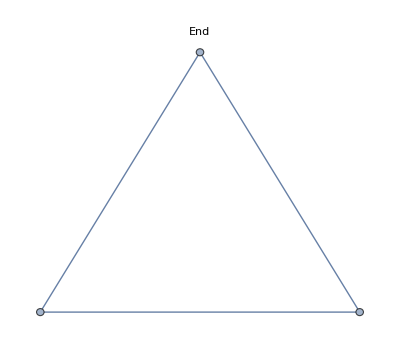

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->Placed[-Graphics-,kp]},PlotLabel->kp],{kp,{"Start","Middle","End"}}]
```

Use explicit coordinates to place labels:

```mathematica
Graphics[{LightBlue,Rectangle[]},ImageSize->50]
```

-Graphics-

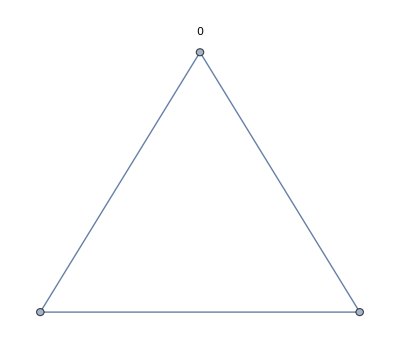
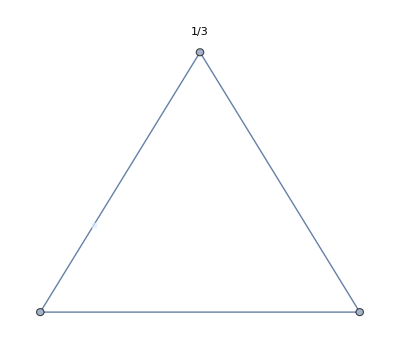
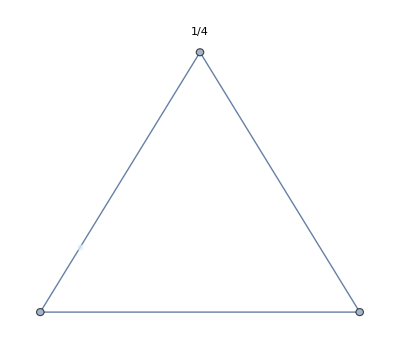

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->Placed[-Graphics-,kp]},PlotLabel->kp,BaselinePosition->Axis],{kp,{0,1/3,1/4}}]
```

Vary positions within the label:

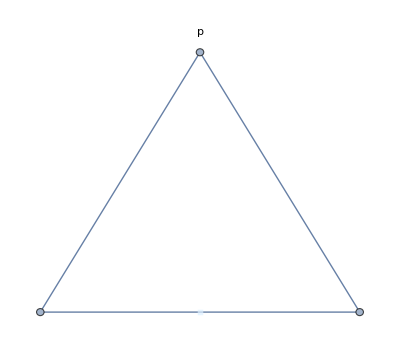
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->3->Placed[-Graphics-,{1/2,kp}]},PlotLabel->p,BaselinePosition->Axis],{kp,{{0,0},{1/2,1/2},{1,1}}}]
```

Place multiple labels using Placed in a wrapper:

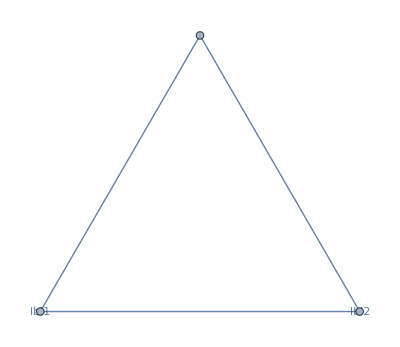

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->1,Placed[{"lbl1","lbl2"},{"Start","End"}]]}]
```

Use automatic labeling by values through Tooltip and StatusArea:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->Placed["Name",Tooltip]]
```

-Graphics-

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->Placed["Name",StatusArea]]
```

-Graphics-

### EdgeShapeFunction

Get a list of build-in settings for EdgeShapeFunction:

```mathematica
ResourceData["EdgeShapeFunction"]
```

{Arrow,BoxLine,CarvedArcArrow,CarvedArrow,DashedLine,DiamondLine,DotLine,DottedLine,FilledArcArrow,FilledArrow,HalfFilledArrow,HalfFilledDoubleArrow,HalfUnfilledArrow,HalfUnfilledDoubleArrow,Line,ShortCarvedArcArrow,ShortCarvedArrow,ShortFilledArcArrow,ShortFilledArrow,ShortUnfilledArcArrow,ShortUnfilledArrow,UnfilledArcArrow,UnfilledArrow}

Undirected edges including the basic line:

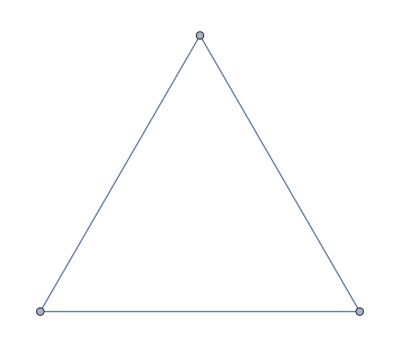

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->"Line"]
```

Lines with different glyphs on the edges:

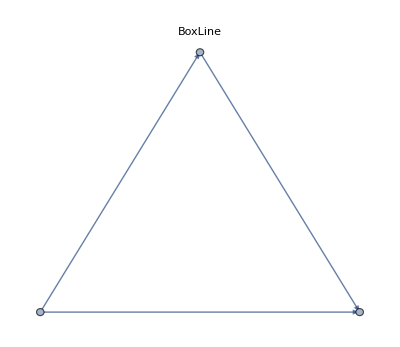
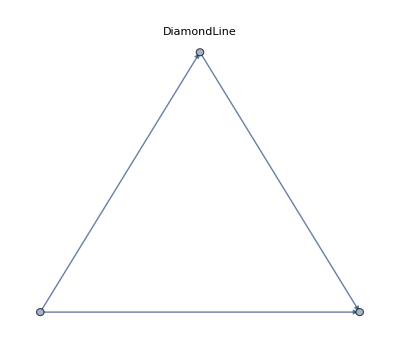
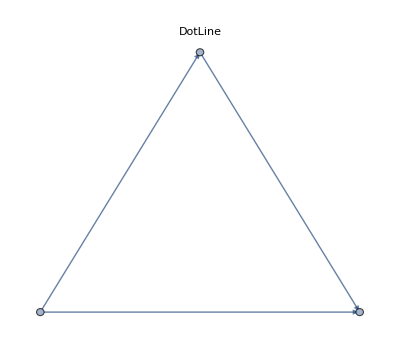

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->kef],{kef,{"BoxLine","DiamondLine","DotLine"}}]
```

Directed edges including solid arrows:

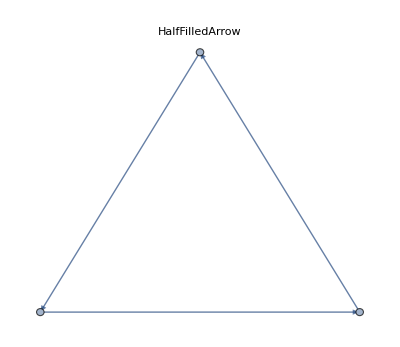
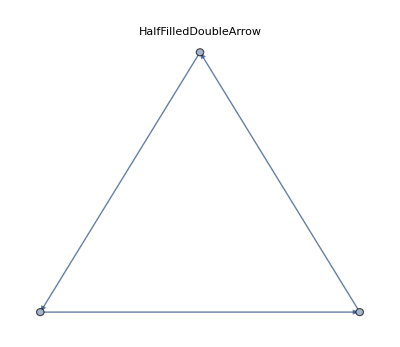
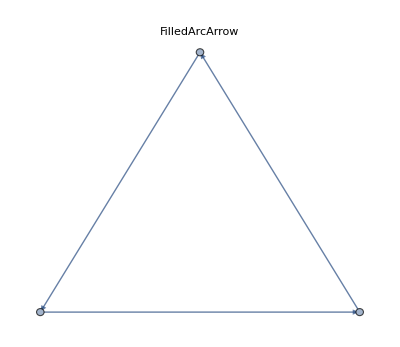
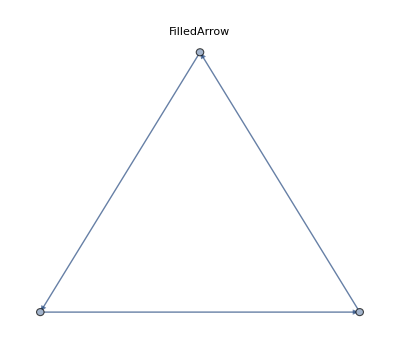
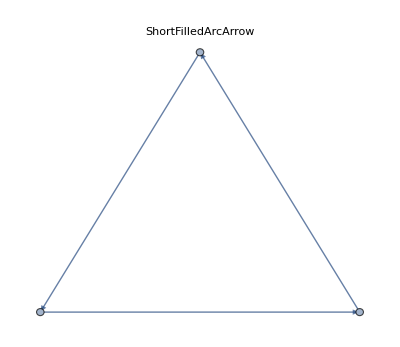
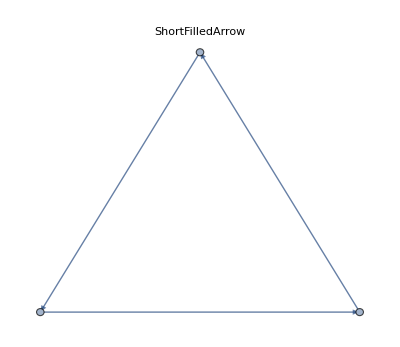

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","FilledArrow"]}]
```

Line arrows:

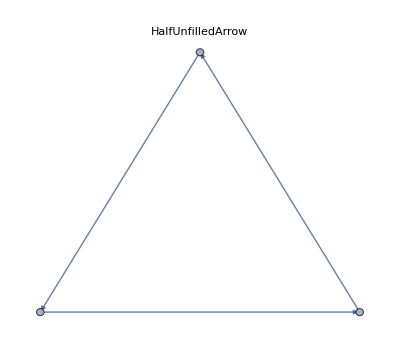
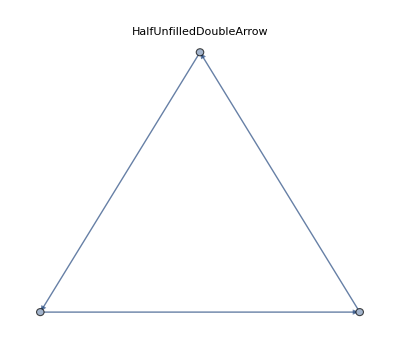
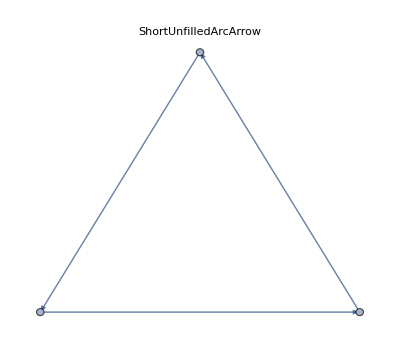
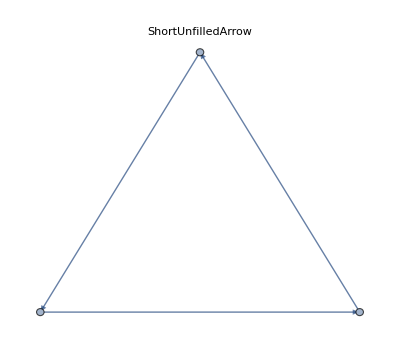
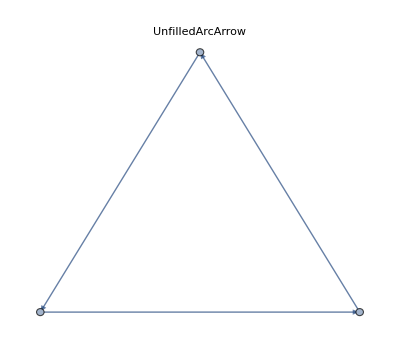
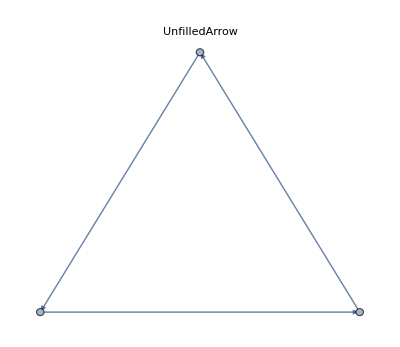

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","UnfilledArrow"]}]
```

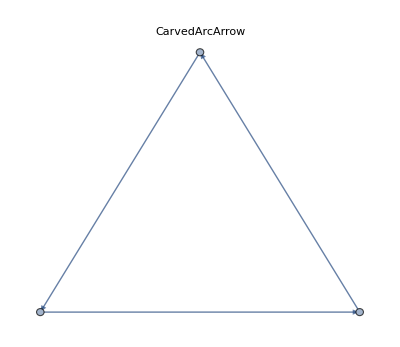
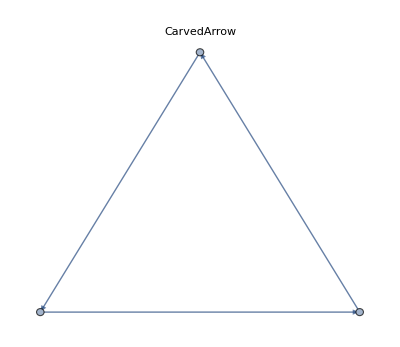
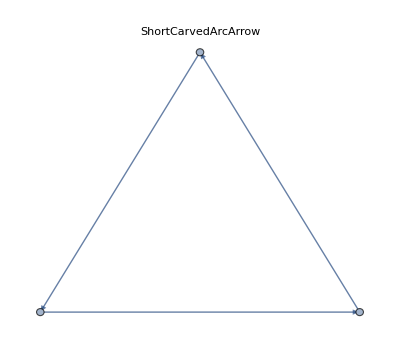
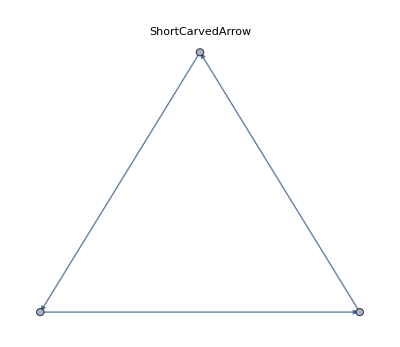

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","CarvedArrow"]}]
```

Specify an edge function for an individual edge:

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->{1->2->"FilledArrow"}]
```

-Graphics-

Combine with a different default edge function:

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->{1->2->"FilledArrow","CarvedArrow"}]
```

-Graphics-

Draw edges by running a program:

```mathematica
ef[pts_List,e_]:=Block[{s=0.015,g=Graphics[Circle[]]},{Arrowheads[{{s,0.33,g},{s,0.67,g}}],Arrow[pts]}]
```

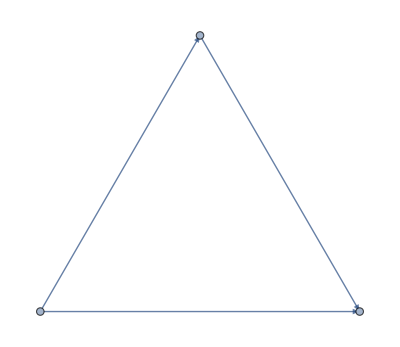

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->ef]
```

EdgeShapeFunction can be combined with EdgeStyle:

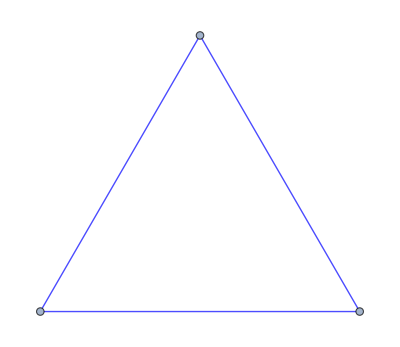

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->(Line[#1]&)]
```

EdgeShapeFunction has higher priority than EdgeStyle:

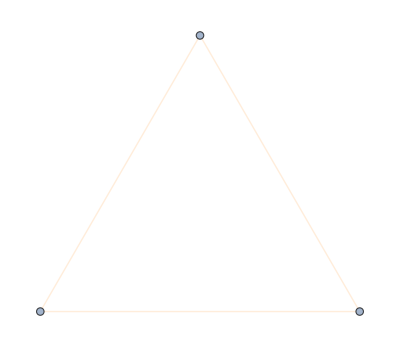

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->({LightOrange,Line[#1]}&)]
```

### EdgeStyle

Style all edges:

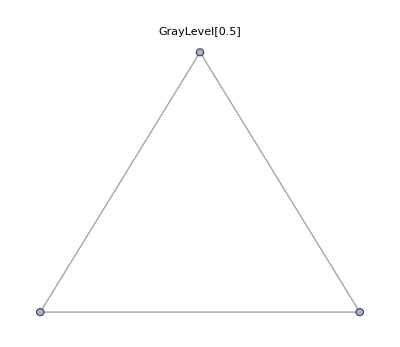
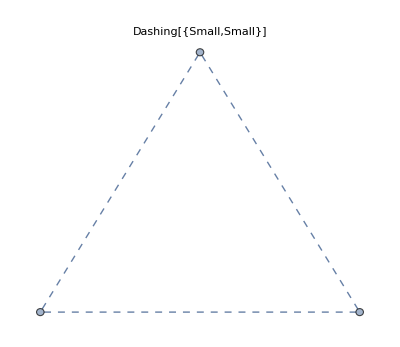
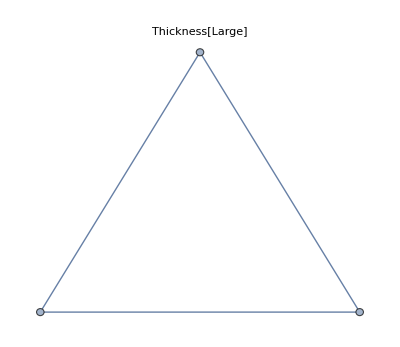

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeStyle->style,PlotLabel->style],{style,{Gray,Dashed,Thick}}]
```

Style individual edges:

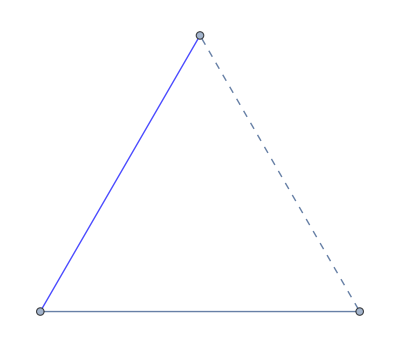

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->{1<->2->Blue,2<->3->Dashed}]
```

EdgeStyle can be combined with EdgeShapeFunction:

```mathematica
efA[el_,___]:=Arrow[el,0.1]
```

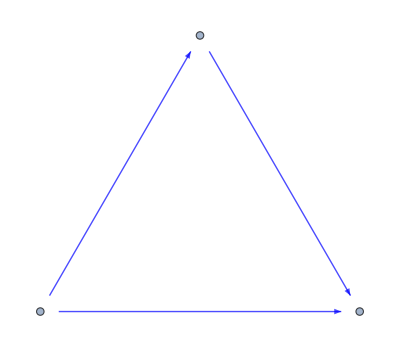

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->efA]
```

EdgeShapeFunction has higher priority than EdgeStyle:

```mathematica
efB[el_,___]:={Red,Arrow[el,0.1]}
```

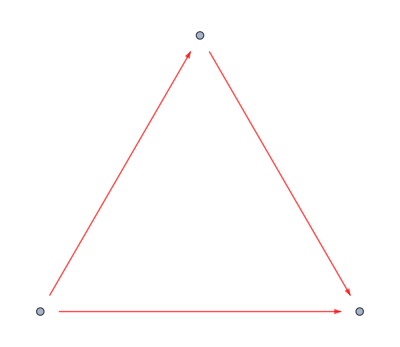

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->efB]
```

EdgeStyle can be combined with BaseStyle:

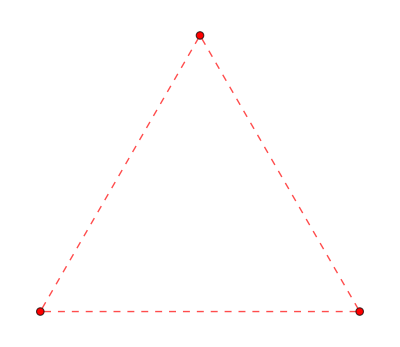

```mathematica
Graph[{1<->2,2<->3,3<->1},BaseStyle->Red,EdgeStyle->Dashed]
```

EdgeStyle has higher priority than BaseStyle:

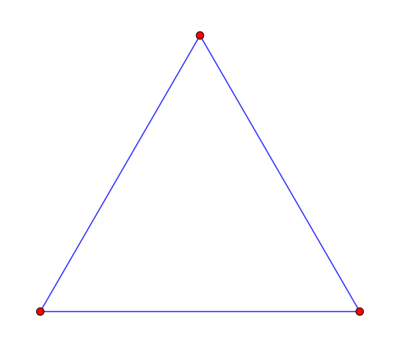

```mathematica
Graph[{1<->2,2<->3,3<->1},BaseStyle->Red,EdgeStyle->Blue]
```

### EdgeWeight

Specify a weight for all edges:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->RandomInteger[5,3]]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[Graph[{1<->2,2<->3,3<->1},EdgeWeight->RandomInteger[5,3]]]//MatrixForm
```

(0 | 3 | 5
3 | 0 | 3
5 | 3 | 0)

Use any numeric expression as a weight:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->{a,b,c}]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[Graph[{1<->2,2<->3,3<->1},EdgeWeight->{a,b,c}]]//MatrixForm
```

(0 | a | c
a | 0 | b
c | b | 0)

### GraphHighlight

Highlight the vertex 1:

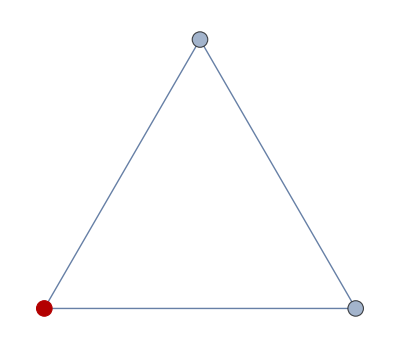

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{1}]
```

Highlight the edge 2<->3:

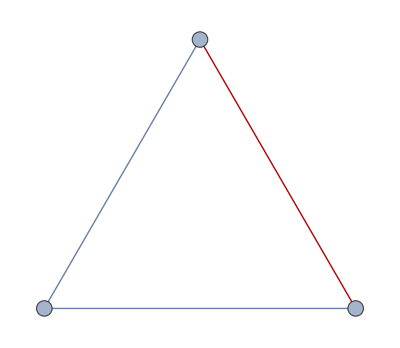

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{2<->3}]
```

Highlight vertices and edges:

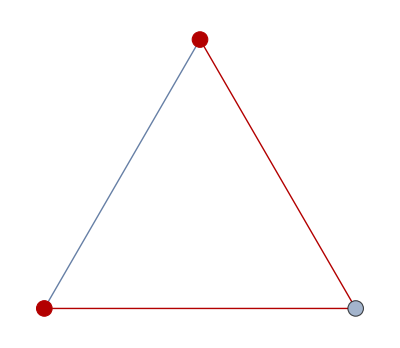

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{1,2,1<->3,2<->3}]
```

### GraphHighlightStyle

Get a list of built-in settings for GraphHighlightStyle:

```mathematica
ResourceData["GraphHighlightStyle"]
```

{Automatic,Dashed,Dotted,Thick,VertexConcaveDiamond,VertexDiamond,VertexTriangle,DehighlightFade,DehighlightGray,DehighlightHide}

Use built-in settings for GraphHighlightStyle:

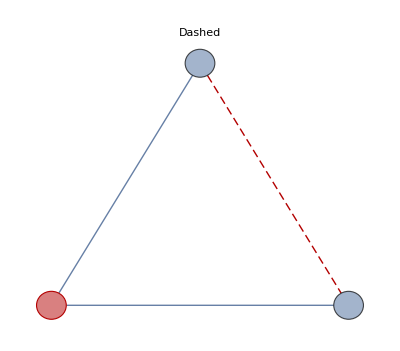
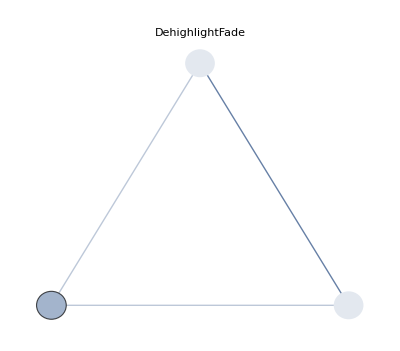
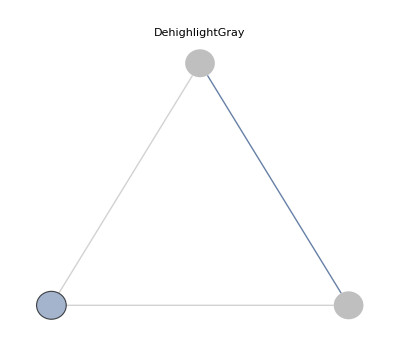
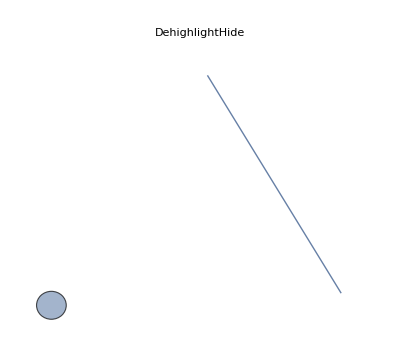
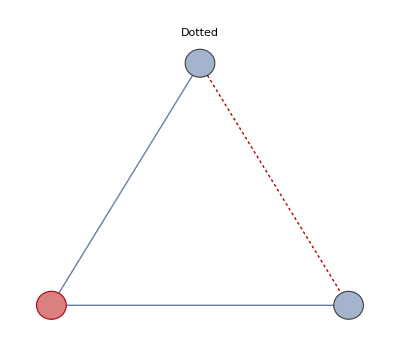
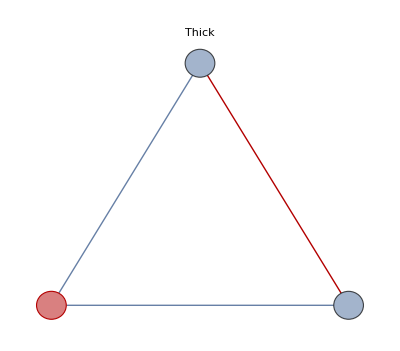
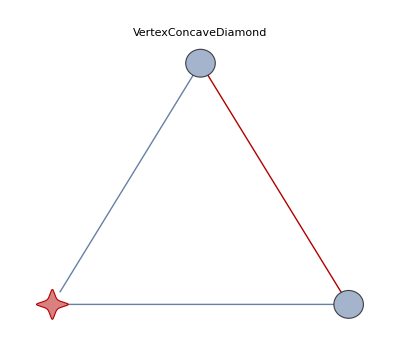
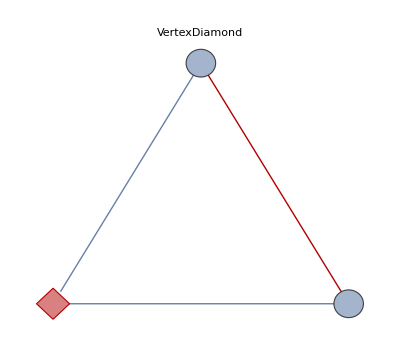

```mathematica
Graph[{1<->2,2<->3,3<->1},GraphHighlight->{1,2<->3},VertexSize->Small,GraphHighlightStyle->#,PlotLabel->#]&/@Complement[ResourceData["GraphHighlightStyle"],{Automatic}]
```

### GraphLayout

By default, the layout is chosen automatically:

```mathematica
Graph[{1<->2,2<->3,3<->1},GraphLayout->Automatic]
```

-Graphics-

Specify layouts on special curves:

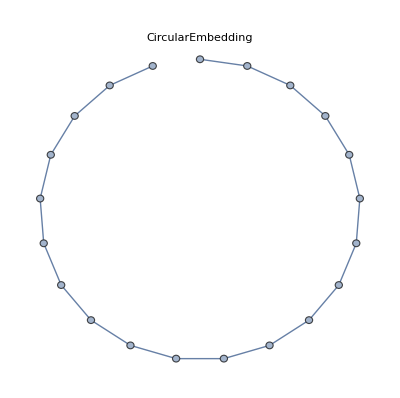
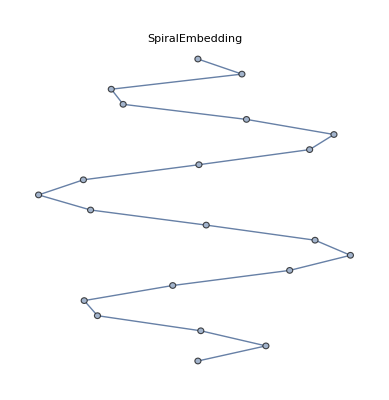

```mathematica
Table[Graph[Table[i<->i+1,{i,20}],GraphLayout->l,PlotLabel->l],{l,{"CircularEmbedding","SpiralEmbedding"}}]
```

Specify layouts that satisfy optimality criteria:

```mathematica
el=EdgeList@GridGraph[{10,10}];
```

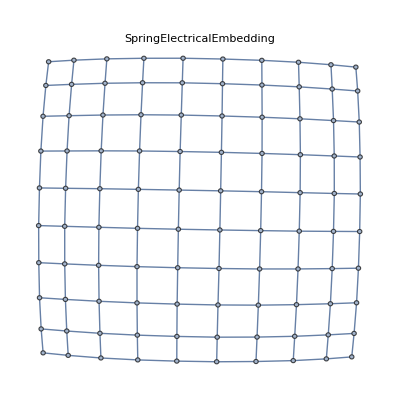
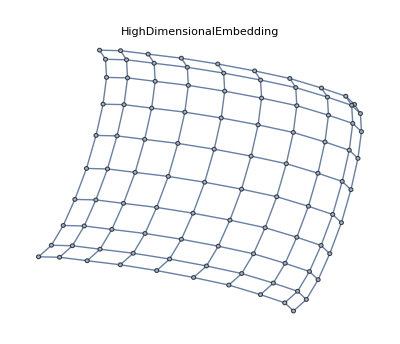
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[el,GraphLayout->l,PlotLabel->Style[l,10]],{l,{"SpringElectricalEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding"}}]
```

VertexCoordinates overrides GraphLayout coordinates:

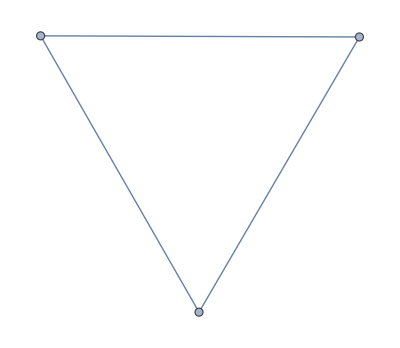
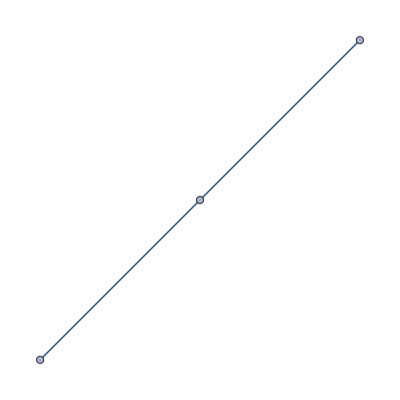

```mathematica
{Graph[{1<->2,2<->3,3<->1},GraphLayout->"SpringElectricalEmbedding"],Graph[{1<->2,2<->3,3<->1},GraphLayout->"SpringElectricalEmbedding",VertexCoordinates->Table[{i,i},{i,0,2}]]}
```

Use AbsoluteOptions to extract VertexCoordinates computed using a layout algorithm:

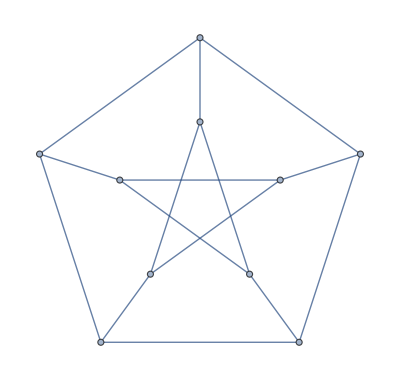

```mathematica
PetersenGraph[]
```

```mathematica
AbsoluteOptions[PetersenGraph[],VertexCoordinates]
```

{VertexCoordinates→{{0.951057,0.309017},{0.587785,-0.809017},{-0.587785,-0.809017},{-0.951057,0.309017},{-2.44929×10^-16,1.},{1.90211,0.618034},{1.17557,-1.61803},{-1.17557,-1.61803},{-1.90211,0.618034},{-4.89859×10^-16,2.}}}

### PlotTheme

#### BaseTheme

Use a common base theme:

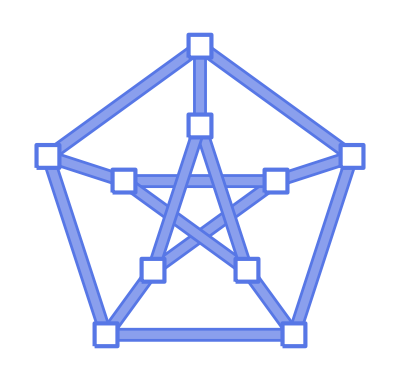

```mathematica
PetersenGraph[PlotTheme->"Business"]
```

Use a monochrome theme:

```mathematica
PetersenGraph[PlotTheme->"Monochrome"]
```

-Graphics-

#### FeatureThemes

Use a large graph theme:

```mathematica
PetersenGraph[PlotTheme->"LargeGraph"]
```

-Graphics-

Use a classic diagram theme:

```mathematica
PetersenGraph[PlotTheme->"ClassicDiagram"]
```

-Graphics-

### VertexCoordinates

By default, any vertex coordinates are computed automatically:

```mathematica
PetersenGraph[]
```

-Graphics-

Extract the resulting vertex coordinates using AbsoluteOptions:

```mathematica
AbsoluteOptions[PetersenGraph[],VertexCoordinates]
```

{VertexCoordinates→{{0.951057,0.309017},{0.587785,-0.809017},{-0.587785,-0.809017},{-0.951057,0.309017},{-2.44929×10^-16,1.},{1.90211,0.618034},{1.17557,-1.61803},{-1.17557,-1.61803},{-1.90211,0.618034},{-4.89859×10^-16,2.}}}

Specify a layout function along an ellipse:

```mathematica
ellipseLayout[n_,{a_,b_}]:=Table[{a Cos[2Pi/n u],b Sin[2Pi/n u]},{u,1,n}]
```

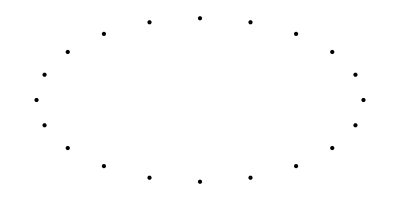

```mathematica
Graphics[Point[ellipseLayout[20,{2,1}]]]
```

Use it to generate vertex coordinates for a graph:

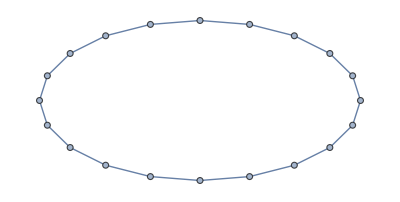

```mathematica
Graph[Table[i<->Mod[i+1,20,1],{i,20}],VertexCoordinates->ellipseLayout[20,{2,1}]]
```

VertexCoordinates has higher priority than GraphLayout:

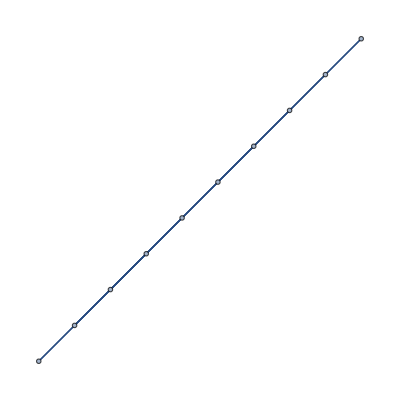

```mathematica
Graph[PetersenGraph[],VertexCoordinates->Table[{i,i},{i,10}],GraphLayout->"CircularEmbedding"]
```

### VertexLabels

Use vertex names as labels:

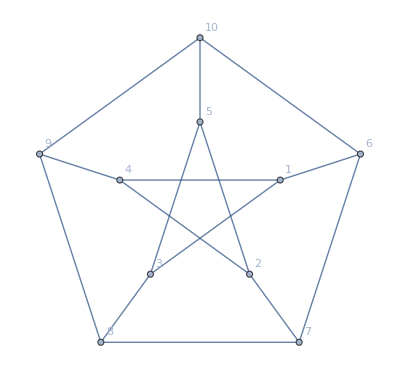

```mathematica
Graph[PetersenGraph[],VertexLabels->"Name"]
```

Label individual vertices:

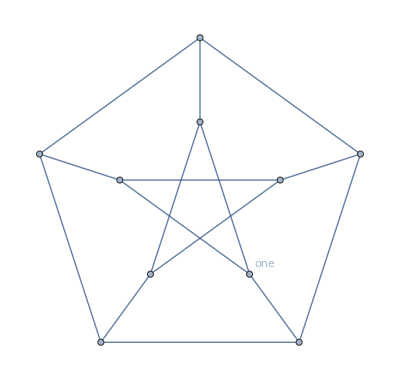

```mathematica
Graph[PetersenGraph[],VertexLabels->{2->"one"}]
```

Label all vertices:

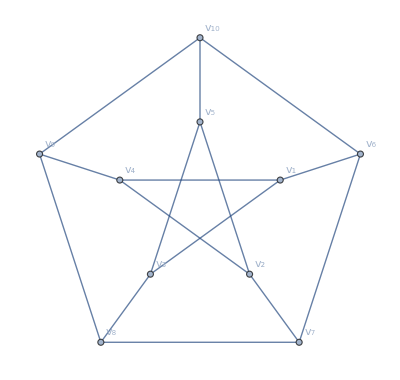

```mathematica
Graph[PetersenGraph[],VertexLabels->Table[i->Subscript[v, i],{i,10}]]
```

Use any expression as a label:

```mathematica
Graph[PetersenGraph[],VertexLabels->{1->-Graphics-,2->-Graphics-,3->-Graphics3D-},ImagePadding->30]
```

-Graphics-

Use Placed with symbolic locations to control label placement, including outside positions:

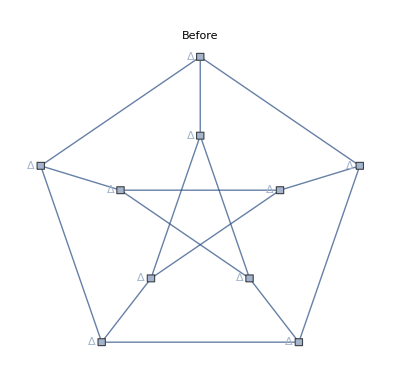
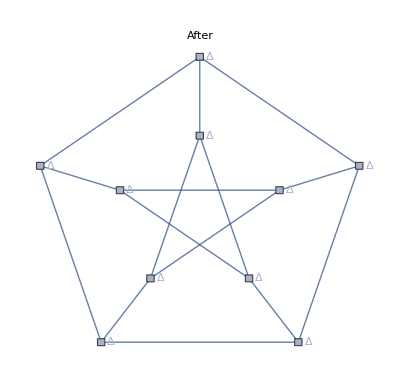
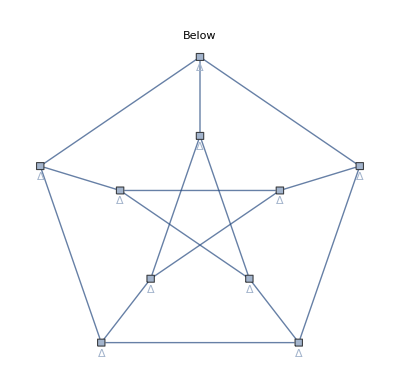
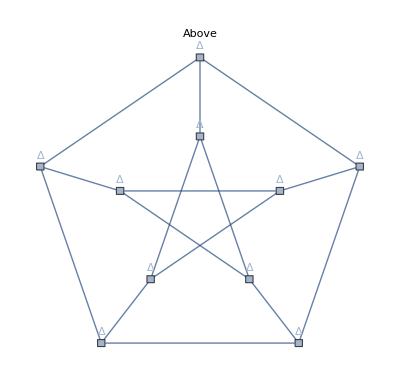

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["Δ",kp],{ki,10}],PlotLabel->kp],{kp,{Before,After,Below,Above}}]
```

Symbolic outside corner positions:

```mathematica
pl={{Before,Below},{After,Below},{Before,Above},{After,Above}};
```

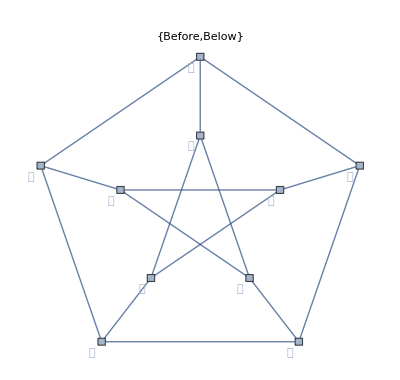
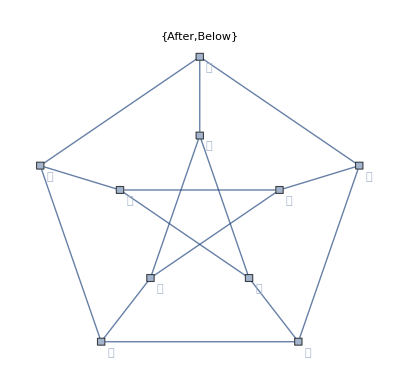
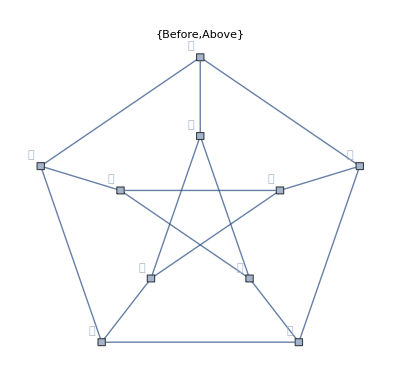
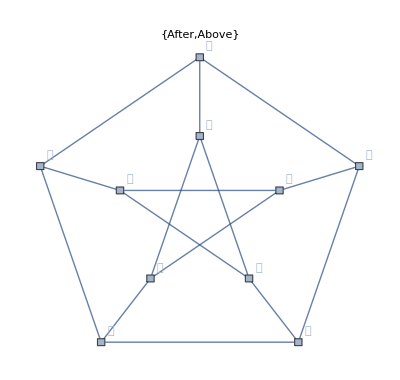

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",kp],{ki,10}],PlotLabel->kp],{kp,pl}]
```

Symbolic inside positions:

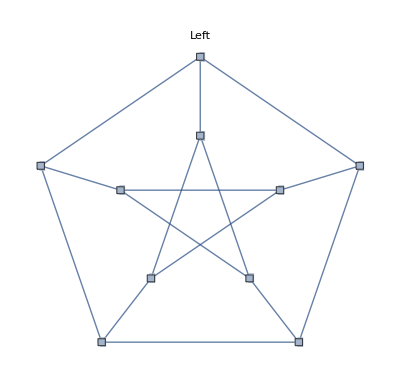
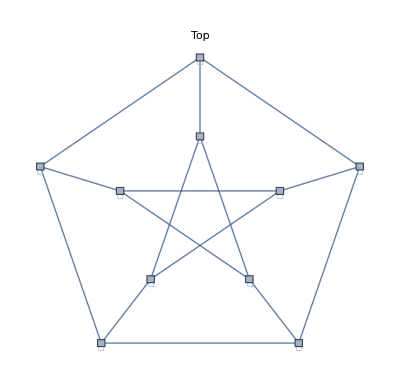
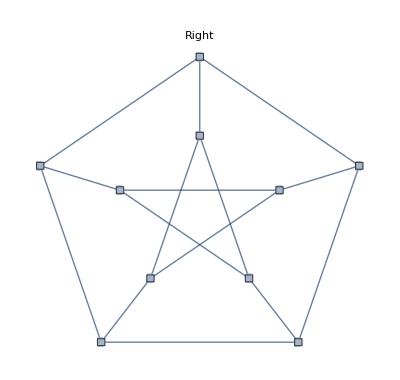
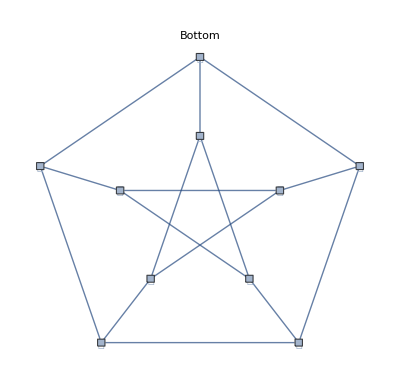

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",kp],{ki,10}],PlotLabel->kp],{kp,{Left,Top,Right,Bottom}}]
```

Symbolic inside corner positions:

```mathematica
plInsideCorners={{Left,Bottom},{Right,Bottom},{Left,Top},{Right,Top}};
```

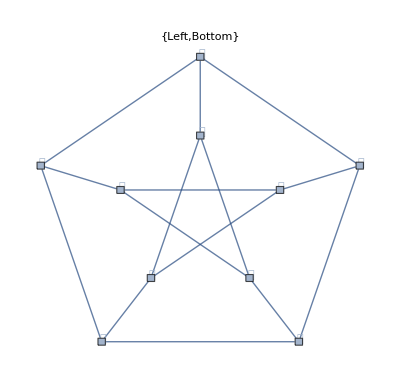
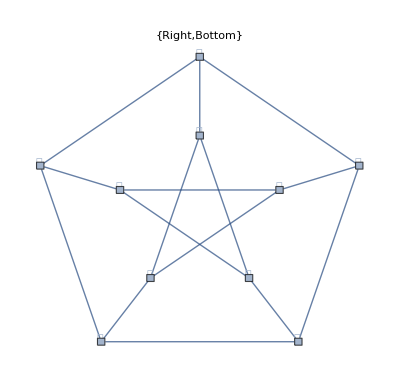
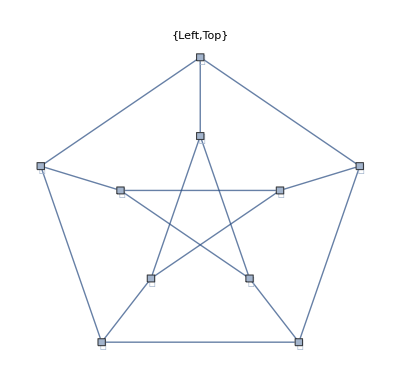
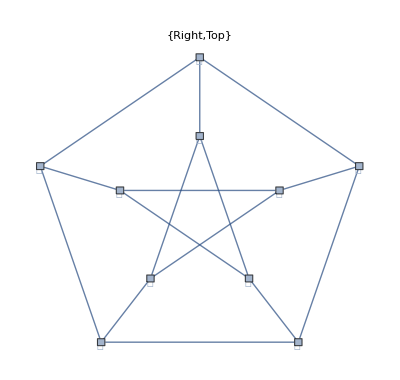

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",kp],{ki,10}],PlotLabel->kp],{kp,plInsideCorners}]
```

Use explicit coordinates to place the center of labels:

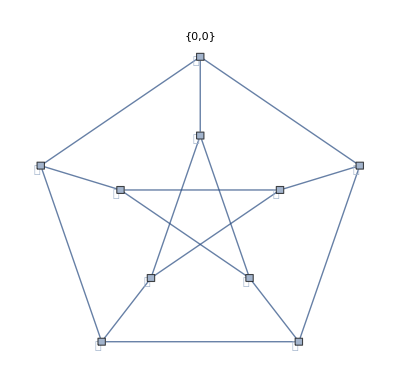
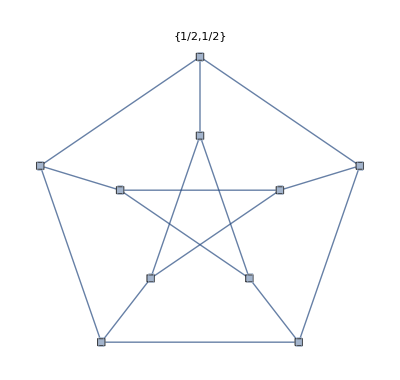
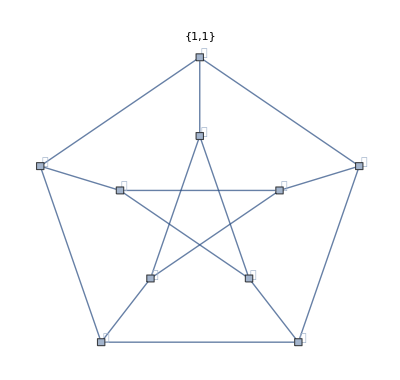

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",kp],{ki,10}],PlotLabel->kp],{kp,{{0,0},{1/2,1/2},{1,1}}}]
```

Place all labels at the upper-right corner of the vertex and vary the coordinates within the label:

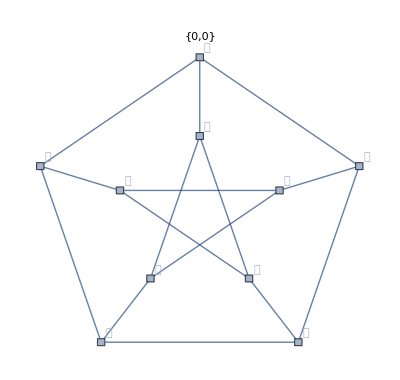
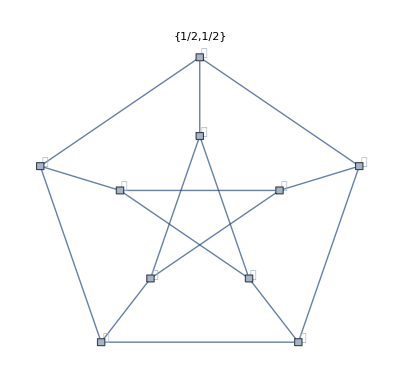
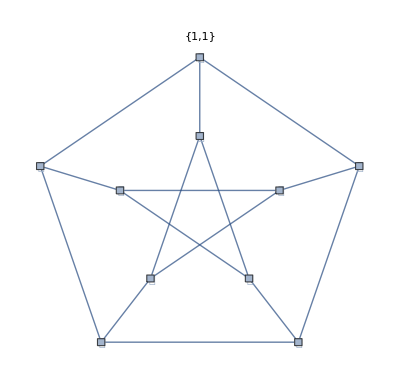

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",{{1,1},kp}],{ki,10}],PlotLabel->kp],{kp,{{0,0},{1/2,1/2},{1,1}}}]
```

Place all labels at the center of vertices:

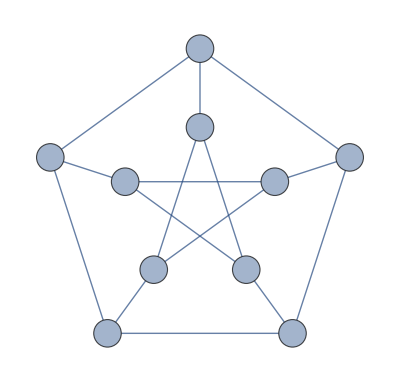

```mathematica
PetersenGraph[VertexSize->0.35,VertexLabels->Placed["𝒢",Center],VertexShapeFunction->"Circle"]
```

Place multiple labels using Place in a wrapper:

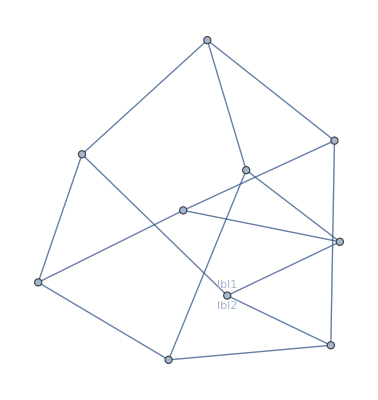

```mathematica
Graph[VertexList@PetersenGraph[]/.{3->Labeled[3,Placed[{"lbl1","lbl2"},{Above,Below}]]},EdgeList@PetersenGraph[]]
```

Place multiple labels using VertexLabels:

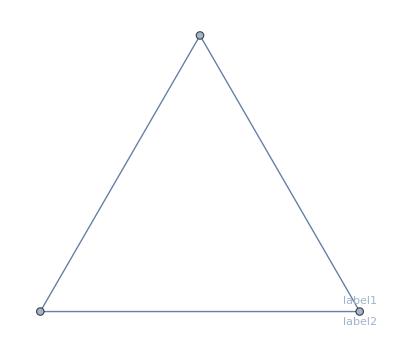

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexLabels->{3->Placed[{"label1","label2"},{Above,Below}]}]
```

Use the argument to Placed to control formatting including Tooltip:

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexLabels->Placed["Name",Tooltip]]
```

-Graphics-

Or StatusArea

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexLabels->Placed["Name",StatusArea]]
```

-Graphics-

Use more elaborate formatting functions:

```mathematica
rotateLabel[label_]:=Rotate[label,45Degree]
```

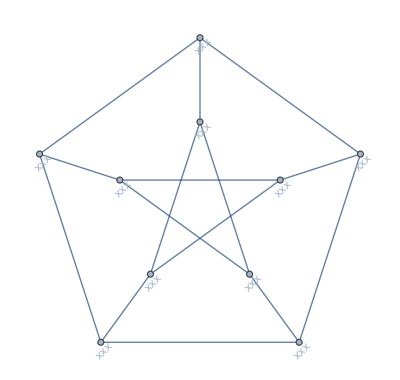

```mathematica
PetersenGraph[VertexLabels->Table[i->Placed["xxx",Below,rotateLabel],{i,10}]]
```

```mathematica
panelLabel[label_]:=Panel[label,FrameMargins->0,Background->Lighter[Yellow,0.7]]
```

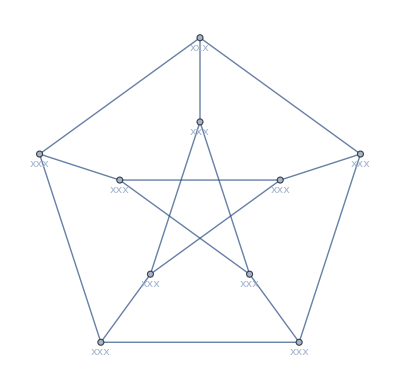

```mathematica
PetersenGraph[VertexLabels->Table[i->Placed["xxx",Below,panelLabel],{i,10}]]
```

```mathematica
hyperlinkLabel[label_]:=Hyperlink[label,"https://en.wikipedia.org/wiki/Petersen_graph"]
```

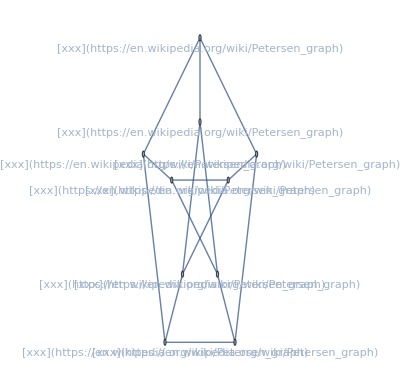

```mathematica
PetersenGraph[VertexLabels->Table[i->Placed["xxx",Below,hyperlinkLabel],{i,10}]]
```

```mathematica
Names["*Function*"]
```

{AbsoluteCorrelationFunction,AmbiguityFunction,AnomalyDetectorFunction,APIFunction,AskFunction,AssessmentFunction,AutocompletionFunction,BezierFunction,BooleanConsecutiveFunction,BooleanCountingFunction,BooleanFunction,BSplineFunction,ButtonFunction,CellEvaluationFunction,CentralMomentGeneratingFunction,ChannelPreSendFunction,ChannelReceiverFunction,CharacteristicFunction,ChartElementDataFunction,ChartElementFunction,ClassifierFunction,CloudFunction,ClusterDissimilarityFunction,ColorDataFunction,ColorFunction,ColorFunctionBinning,ColorFunctionScaling,CombinerFunction,CompiledCodeFunction,CompiledFunction,ComplexityFunction,ConnectLibraryCallbackFunction,ContentDetectorFunction,ContentLocationFunction,CookieFunction,CopyFunction,CorrelationFunction,CounterFunction,CovarianceEstimatorFunction,CovarianceFunction,CriterionFunction,CumulantGeneratingFunction,CylindricalDecompositionFunction,DateFunction,DefineResourceFunction,DeliveryFunction,DimensionReducerFunction,DispersionEstimatorFunction,DisplayFunction,DistanceFunction,EchoFunction,EdgeRenderingFunction,EdgeShapeFunction,EntityFunction,EpilogFunction,ExponentFunction,ExponentialGeneratingFunction,ExtentElementFunction,ExternalFunction,ExternalFunctionName,FactorialMomentGeneratingFunction,FeatureExtractorFunction,FetchReferencedFunctions,FieldCompletionFunction,FindGeneratingFunction,FindSequenceFunction,FormFunction,FormLayoutFunction,Function,FunctionAnalytic,FunctionBijective,FunctionCompile,FunctionCompileExport,FunctionCompileExportByteArray,FunctionCompileExportLibrary,FunctionCompileExportString,FunctionContinuous,FunctionConvexity,FunctionDeclaration,FunctionDiscontinuities,FunctionDomain,FunctionExpand,FunctionInjective,FunctionInterpolation,FunctionLayer,FunctionMeromorphic,FunctionMonotonicity,FunctionPeriod,FunctionPoles,FunctionRange,FunctionSign,FunctionSingularities,FunctionSpace,FunctionSurjective,GaugeFaceElementFunction,GaugeFrameElementFunction,GeneratingFunction,GeoStylingImageFunction,GreenFunction,GuidePageInlineListingFunction,GuidePageOneLineFunction,HandlerFunctions,HandlerFunctionsKeys,HazardFunction,HeaderDisplayFunction,ImageCaptureFunction,ImagePreviewFunction,InsertionFunction,InterpolatingFunction,InterpretationFunction,InverseFunction,InverseFunctions,InverseSurvivalFunction,ItemDisplayFunction,KernelFunction,KeyCollisionFunction,LabelingFunction,LayerSizeFunction,LegendFunction,LibraryFunction,LibraryFunctionDeclaration,LibraryFunctionError,LibraryFunctionInformation,LibraryFunctionLoad,LibraryFunctionUnload,LinearOffsetFunction,LinearSolveFunction,LinkFunction,LossFunction,MailReceiverFunction,MailResponseFunction,MathematicalFunctionData,MatrixFunction,MergingFunction,MeshCellShapeFunction,MeshFunctions,MeshRefinementFunction,MomentGeneratingFunction,MultilineFunction,NearestFunction,NormalsFunction,NormFunction,NotificationFunction,NumericFunction,OpacityFunction,OpacityFunctionScaling,OpenFunctionInspectorPacket,ParametricFunction,ParentEdgeLabelFunction,ParentEdgeShapeFunction,ParentEdgeStyleFunction,PartialCorrelationFunction,PersistResourceFunction,PointDensityFunction,PointStatisticFunction,PredictorFunction,RandomFunction,RationalFunctions,RecalibrationFunction,RegionDistanceFunction,RegionFunction,RegionMemberFunction,RegionNearestFunction,ResourceFunction,ReturnReceiptFunction,SampledSoundFunction,ScalingFunctions,SequencePredictorFunction,SetSharedFunction,ShortestPathFunction,SpatialEstimatorFunction,SpatialTrendFunction,StreamColorFunction,StreamColorFunctionScaling,SurvivalFunction,TargetFunctions,TextResourceFunction,TextureCoordinateFunction,TrackingFunction,TraditionalFunctionNotation,TrainingProgressFunction,TransferFunctionCancel,TransferFunctionExpand,TransferFunctionFactor,TransferFunctionModel,TransferFunctionPoles,TransferFunctionTransform,TransferFunctionZeros,TransformationFunction,TransformationFunctions,TreeElementLabelFunction,TreeElementShapeFunction,TreeElementSizeFunction,TreeElementStyleFunction,UtilityFunction,ValuePreprocessingFunction,VarianceEstimatorFunction,VariogramFunction,VectorColorFunction,VectorColorFunctionScaling,VertexRenderingFunction,VertexShapeFunction,WordSelectionFunction,$AllowExternalChannelFunctions,$AssertFunction,$DisplayFunction,$SharedFunctions,$SoundDisplayFunction}